0.570381 (-0.136+x)+416.289 (-0.136+x)^2+60972.1 (-0.136+x)^3-2.29352×10^6 (-0.136+x)^4+2.08245×10^7 (-0.136+x)^5

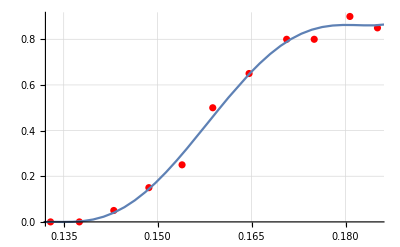

```mathematica
vec = Import["/home/syx/SYXrepo/vacation_homework/percolation/data/1000.txt","Data"];
data = vec[[All,{1,2}]];
(*data = Select[data,#[[2]]<0.99 && #[[2]]>0 &];*)
(*datl = Table[{data[[i,1]],Log[data[[i,2]]]},{i,1,Length[data]}];*)
a=0.136;fit = Fit[data, {(x-a),(x-a)^2,(x-a)^3,(x-a)^4,(x-a)^5},x]
fig = Show[ListPlot[data, PlotStyle->Red, PlotTheme->"Grid"], Plot[fit, {x, 0, 5}]]
(*ListPlot[data, PlotStyle->Thick, PlotTheme->"Grid"]*)
```

```mathematica
Export["/home/syx/SYXrepo/vacation_homework/percolation/img/fig_1.jpg",fig,"JPEG",ImageResolution->500]
Import[%]
```